# The Luttinger-Tisza Method for J_1 -J_2 Triangular Lattice Anti-ferromagnet

## The Minimization function

```mathematica
e1={1,0};
e2={(1/2),Sqrt[3]/2};
e3={-(1/2),Sqrt[3]/2};
e4={(√3)/2,1/2};
e5={0,1};
e6={-(√3)/2,1/2};

F[qx_,qy_,alpha_]:=0Cos[qx]+2Cos[qx/2]Cos[(qy √3)/2]+alpha(Cos[qy √3]+2Cos[3 qx/2]Cos[(qy √3)/2])
```

```mathematica
Plot3D[F[qx,qy,0.0],{qx,-2Pi,2 Pi},{qy,-2Pi,2 Pi},PlotLegends->True,ViewPoint->Top]
```

-Graphics3D-

## Anomalous dipole density

### For uniform lattice

```mathematica
F[qx_,qy_]:=Cos[qx]+2Cos[qx/2]Cos[(qy√3)/2]
```

```mathematica
S1[a_,b_]:=D[F[x,y],x]/.{x->a,y-> b}
```

```mathematica
S2[a_,b_]:=D[F[x,y],y]/.{x->a,y-> b}
```

```mathematica
Fxx[a_,b_]:=D[F[x,y],{x,2}]/.{x->a,y-> b}
```

```mathematica
Fxy[a_,b_]:=D[F[x,y],x,y]/.{x->a,y-> b}
```

```mathematica
Fyy[a_,b_]:=D[F[x,y],{y,2}]/.{x->a,y-> b}
```

```mathematica
FindMinimum[{F[a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

{-1.5,{a→2.0944,b→3.6276}}

```mathematica
SOLN1=Solve[S1[a,b]==0&&S2[a,b]==0,{a,b}]
```

{{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-(2 π)/3+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/3+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/3+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 ((2 π)/3+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]}}

```mathematica
SOLN2=SOLN1/.{C[1]->0,C[2]->0}
```

{{a→0,b→0},{a→0,b→(2 π)/(√3)},{a→-(4 π)/3,b→0},{a→-π,b→-π/(√3)},{a→-π,b→π/(√3)},{a→-(2 π)/3,b→(2 π)/(√3)},{a→(2 π)/3,b→(2 π)/(√3)},{a→π,b→-π/(√3)},{a→π,b→π/(√3)},{a→(4 π)/3,b→0},{a→2 π,b→0},{a→2 π,b→(2 π)/(√3)}}

```mathematica
F[a,b]/.SOLN2
```

{3,-1,-3/2,-1,-1,-3/2,-3/2,-1,-1,-3/2,-1,3}

```mathematica
Fxx[a,b]/.SOLN2
```

{-3/2,-1/2,3/4,1,1,3/4,3/4,1,1,3/4,-1/2,-3/2}

```mathematica
Fyy[a,b]/.SOLN2
```

{-3/2,3/2,3/4,0,0,3/4,3/4,0,0,3/4,3/2,-3/2}

```mathematica
Fxx[a,b]Fyy[a,b]-Fxy[a,b]^2/.SOLN2
```

{9/4,-3/4,9/16,-3/4,-3/4,9/16,9/16,-3/4,-3/4,9/16,-3/4,9/4}

```mathematica
Plot3D[F[x,y,0],{x,0,2π},{y,0,2π},ViewPoint->Top]
```

-Graphics3D-

### For anomalous dipole along (1,0)

```mathematica
F[qx_,qy_]:=2Cos[qx/2]Cos[(qy√3)/2]
```

```mathematica
S1[a_,b_]:=D[F[x,y],x]/.{x->a,y-> b}
```

```mathematica
S2[a_,b_]:=D[F[x,y],y]/.{x->a,y-> b}
```

```mathematica
Fxx[a_,b_]:=D[F[x,y],{x,2}]/.{x->a,y-> b}
```

```mathematica
Fxy[a_,b_]:=D[F[x,y],x,y]/.{x->a,y-> b}
```

```mathematica
Fyy[a_,b_]:=D[F[x,y],{y,2}]/.{x->a,y-> b}
```

```mathematica
FindMinimum[{F[a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

{-2.,{a→-5.4598×10^-10,b→3.6276}}

```mathematica
SOLN1=Solve[S1[a,b]==0&&S2[a,b]==0,{a,b}]
```

{{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]}}

```mathematica
SOLN2=SOLN1/.{C[1]->0,C[2]->0}
```

{{a→0,b→0},{a→0,b→(2 π)/(√3)},{a→-π,b→-π/(√3)},{a→-π,b→π/(√3)},{a→π,b→-π/(√3)},{a→π,b→π/(√3)},{a→2 π,b→0},{a→2 π,b→(2 π)/(√3)}}

```mathematica
F[a,b]/.SOLN2
```

{2,-2,0,0,0,0,-2,2}

```mathematica
Fxx[a,b]/.SOLN2
```

{-1/2,1/2,0,0,0,0,1/2,-1/2}

```mathematica
Fyy[a,b]/.SOLN2
```

{-3/2,3/2,0,0,0,0,3/2,-3/2}

```mathematica
Fxx[a,b]Fyy[a,b]-Fxy[a,b]^2/.SOLN2
```

{3/4,3/4,-3/4,-3/4,-3/4,-3/4,3/4,3/4}

```mathematica
Plot3D[F[x,y,0],{x,0,2π},{y,0,2π},ViewPoint->Top]
```

-Graphics3D-

### For anomalous dipole along (1/2,(√3)/2)

```mathematica
F[qx_,qy_]:=Cos[qx]+Cos[(qx+√3 qy)/2]
```

```mathematica
S1[a_,b_]:=D[F[x,y],x]/.{x->a,y-> b}
```

```mathematica
S2[a_,b_]:=D[F[x,y],y]/.{x->a,y-> b}
```

```mathematica
Fxx[a_,b_]:=D[F[x,y],{x,2}]/.{x->a,y-> b}
```

```mathematica
Fxy[a_,b_]:=D[F[x,y],x,y]/.{x->a,y-> b}
```

```mathematica
Fyy[a_,b_]:=D[F[x,y],{y,2}]/.{x->a,y-> b}
```

```mathematica
FindMinimum[{F[a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

{-2.,{a→3.14159,b→1.8138}}

```mathematica
SOLN1=Solve[S1[a,b]==0&&S2[a,b]==0,{a,b}]
```

{{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]}}

```mathematica
SOLN2=SOLN1/.{C[1]->0,C[2]->0}
```

{{a→0,b→0},{a→0,b→(2 π)/(√3)},{a→-π,b→-π/(√3)},{a→-π,b→π/(√3)},{a→π,b→-π/(√3)},{a→π,b→π/(√3)},{a→2 π,b→0},{a→2 π,b→(2 π)/(√3)}}

```mathematica
F[a,b]/.SOLN2
```

{2,0,-2,0,0,-2,0,2}

```mathematica
Fxx[a,b]/.SOLN2
```

{-5/4,-3/4,5/4,3/4,3/4,5/4,-3/4,-5/4}

```mathematica
Fyy[a,b]/.SOLN2
```

{-3/4,3/4,3/4,-3/4,-3/4,3/4,3/4,-3/4}

```mathematica
Fxx[a,b]Fyy[a,b]-Fxy[a,b]^2/.SOLN2
```

{3/4,-3/4,3/4,-3/4,-3/4,3/4,-3/4,3/4}

```mathematica
Plot3D[F[x,y,0],{x,0,2π},{y,0,2π},ViewPoint->Top]
```

-Graphics3D-

### For anomalous dipole along (-1/2,(√3)/2)

```mathematica
F[qx_,qy_]:=Cos[qx]+Cos[(-qx+√3 qy)/2]
```

```mathematica
S1[a_,b_]:=D[F[x,y],x]/.{x->a,y-> b}
```

```mathematica
S2[a_,b_]:=D[F[x,y],y]/.{x->a,y-> b}
```

```mathematica
Fxx[a_,b_]:=D[F[x,y],{x,2}]/.{x->a,y-> b}
```

```mathematica
Fxy[a_,b_]:=D[F[x,y],x,y]/.{x->a,y-> b}
```

```mathematica
Fyy[a_,b_]:=D[F[x,y],{y,2}]/.{x->a,y-> b}
```

```mathematica
FindMinimum[{F[a,b],√(a^2+b^2)≤ 2π},{a,b}]
```

{-2.,{a→3.14159,b→-1.8138}}

```mathematica
SOLN1=Solve[S1[a,b]==0&&S2[a,b]==0,{a,b}]
```

{{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]}}

```mathematica
SOLN2=SOLN1/.{C[1]->0,C[2]->0}
```

{{a→0,b→0},{a→0,b→(2 π)/(√3)},{a→-π,b→-π/(√3)},{a→-π,b→π/(√3)},{a→π,b→-π/(√3)},{a→π,b→π/(√3)},{a→2 π,b→0},{a→2 π,b→(2 π)/(√3)}}

```mathematica
F[a,b]/.SOLN2
```

{2,0,0,-2,-2,0,0,2}

```mathematica
Fxx[a,b]/.SOLN2
```

{-5/4,-3/4,3/4,5/4,5/4,3/4,-3/4,-5/4}

```mathematica
Fyy[a,b]/.SOLN2
```

{-3/4,3/4,-3/4,3/4,3/4,-3/4,3/4,-3/4}

```mathematica
Fxx[a,b]Fyy[a,b]-Fxy[a,b]^2/.SOLN2
```

{3/4,-3/4,-3/4,3/4,3/4,-3/4,-3/4,3/4}

```mathematica
Plot3D[F[x,y,0],{x,0,2π},{y,0,2π},ViewPoint->Top]
```

-Graphics3D-

### Coupling anisotropy along (1,0)

```mathematica
F[qx_,qy_,t_]:=(1+t)Cos[qx]+2Cos[qx/2]Cos[(qy √3)/2]
```

```mathematica
S1[a_,b_,t_]:=D[F[x,y,t],x]/.{x->a,y-> b}
```

```mathematica
S2[a_,b_,t_]:=D[F[x,y,t],y]/.{x->a,y-> b}
```

```mathematica
Fxx[a_,b_,t_]:=D[F[x,y,t],{x,2}]/.{x->a,y-> b}
```

```mathematica
Fxy[a_,b_,t_]:=D[F[x,y,t],x,y]/.{x->a,y-> b}
```

```mathematica
Fyy[a_,b_,t_]:=D[F[x,y,t],{y,2}]/.{x->a,y-> b}
```

```mathematica
FindMinimum[{F[a,b,0.1],√(a^2+b^2)≤ 2π},{a,b}]
```

{-1.55455,{a→2.19787,b→3.6276}}

```mathematica
SOLN1=Solve[S1[a,b,t]==0&&S2[a,b,t]==0,{a,b}]
```

{{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[4 π C[1],C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (-π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (-π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π/2+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π/2+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(4 π C[2])/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (π+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (π+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (ArcTan[-1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (ArcTan[1/(√((1+t)^2))+t/(√((1+t)^2)),0]+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (ArcTan[-1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (ArcTan[1/(√((1+t)^2))+t/(√((1+t)^2)),0]+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (ArcTan[1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (ArcTan[-1/(√((1+t)^2))-t/(√((1+t)^2)),0]+2 π C[2]))/(√3),C[2]∈Integers]},{a→ConditionalExpression[2 (ArcTan[1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]+2 π C[1]),C[1]∈Integers],b→ConditionalExpression[(2 (ArcTan[-1/(√((1+t)^2))-t/(√((1+t)^2)),0]+2 π C[2]))/(√3),C[2]∈Integers]}}

```mathematica
SOLN2=SOLN1/.{C[1]->0,C[2]->0}
```

{{a→0,b→0},{a→0,b→(2 π)/(√3)},{a→-π,b→-π/(√3)},{a→-π,b→π/(√3)},{a→π,b→-π/(√3)},{a→π,b→π/(√3)},{a→2 π,b→0},{a→2 π,b→(2 π)/(√3)},{a→2 ArcTan[-1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))],b→(2 ArcTan[1/(√((1+t)^2))+t/(√((1+t)^2)),0])/(√3)},{a→2 ArcTan[-1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))],b→(2 ArcTan[1/(√((1+t)^2))+t/(√((1+t)^2)),0])/(√3)},{a→2 ArcTan[1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))],b→(2 ArcTan[-1/(√((1+t)^2))-t/(√((1+t)^2)),0])/(√3)},{a→2 ArcTan[1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))],b→(2 ArcTan[-1/(√((1+t)^2))-t/(√((1+t)^2)),0])/(√3)}}

```mathematica
F[a,b,t]/.SOLN2
```

{3+t,-1+t,-1-t,-1-t,-1-t,-1-t,-1+t,3+t,-(2 (1/(√((1+t)^2))+t/(√((1+t)^2))))/(√(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))+(1+t) Cos[2 ArcTan[-1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]],-(2 (1/(√((1+t)^2))+t/(√((1+t)^2))))/(√(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))+(1+t) Cos[2 ArcTan[-1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]],(2 (-1/(√((1+t)^2))-t/(√((1+t)^2))))/(√(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))+(1+t) Cos[2 ArcTan[1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]],(2 (-1/(√((1+t)^2))-t/(√((1+t)^2))))/(√(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))+(1+t) Cos[2 ArcTan[1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]]}

```mathematica
F[a,b,t]/.SOLN2/.t-> 0.01
```

{3.01,-0.99,-1.01,-1.01,-1.01,-1.01,-0.99,3.01,-1.50505,-1.50505,-1.50505,-1.50505}

```mathematica
Fxx[a,b,t]/.SOLN2
```

{-3/2-t,-1/2-t,1+t,1+t,1+t,1+t,-1/2-t,-3/2-t,(1/(√((1+t)^2))+t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[-1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]],(1/(√((1+t)^2))+t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[-1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]],-(-1/(√((1+t)^2))-t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]],-(-1/(√((1+t)^2))-t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]]}

```mathematica
Fxx[a,b,t]/.SOLN2/.t-> 0.1
```

{-1.6,-0.6,1.1,1.1,1.1,1.1,-0.6,-1.6,0.872727,0.872727,0.872727,0.872727}

```mathematica
Fyy[a,b,t]/.SOLN2
```

{-3/2,3/2,0,0,0,0,3/2,-3/2,(3 (1/(√((1+t)^2))+t/(√((1+t)^2))))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2))),(3 (1/(√((1+t)^2))+t/(√((1+t)^2))))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2))),-(3 (-1/(√((1+t)^2))-t/(√((1+t)^2))))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2))),-(3 (-1/(√((1+t)^2))-t/(√((1+t)^2))))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))}

```mathematica
Fyy[a,b,t]/.SOLN2/.t-> 0.1
```

{-3/2,3/2,0,0,0,0,3/2,-3/2,0.681818,0.681818,0.681818,0.681818}

```mathematica
Fxx[a,b,t]Fyy[a,b,t]-Fxy[a,b,t]^2/.SOLN2
```

{-3/2 (-3/2-t),3/2 (-1/2-t),-3/4,-3/4,-3/4,-3/4,3/2 (-1/2-t),-3/2 (-3/2-t),(3 (1/(√((1+t)^2))+t/(√((1+t)^2))) ((1/(√((1+t)^2))+t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[-1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]]))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2))),(3 (1/(√((1+t)^2))+t/(√((1+t)^2))) ((1/(√((1+t)^2))+t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[-1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]]))/(2 √(4+8 t+4 t^2) √((1/(√((1+t)^2))+t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2))),-(3 (-1/(√((1+t)^2))-t/(√((1+t)^2))) (-(-1/(√((1+t)^2))-t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[1/(√(4+8 t+4 t^2)),-(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]]))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2))),-(3 (-1/(√((1+t)^2))-t/(√((1+t)^2))) (-(-1/(√((1+t)^2))-t/(√((1+t)^2)))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))-(1+t) Cos[2 ArcTan[1/(√(4+8 t+4 t^2)),(√(3+8 t+4 t^2))/(√(4+8 t+4 t^2))]]))/(2 √(4+8 t+4 t^2) √((-1/(√((1+t)^2))-t/(√((1+t)^2)))^2) √(1/(4+8 t+4 t^2)+(3+8 t+4 t^2)/(4+8 t+4 t^2)))}

```mathematica
Fxx[a,b,t]Fyy[a,b,t]-Fxy[a,b,t]^2/.SOLN2/.t-> 0.1
```

{2.4,-0.9,-3/4,-3/4,-3/4,-3/4,-0.9,2.4,0.595041,0.595041,0.595041,0.595041}

```mathematica
Plot3D[F[x,y,0],{x,0,2π},{y,0,2π},ViewPoint->Top]
```

-Graphics3D-

### Perturbative treatment for (1,0)

```mathematica
F[qx_,qy_,t_]:=(1+t)Cos[qx]+2Cos[qx/2]Cos[(qy √3)/2]
```

```mathematica
F[(4π)/3+x,y,t]
```

2 Cos[1/2 ((4 π)/3+x)] Cos[(√3 y)/2]-(1+t) Sin[π/6-x]

```mathematica
Normal[Series[F[(4π)/3+x,y,t],{x,0,2},{y,0,2},{t,0,2}]]
```

-3/2+(3 x^2)/8+t (-1/2+(√3 x)/2+x^2/4)+(3/8+(3 √3 x)/16-(3 x^2)/64) y^2

### Perturbative treatment for (1/2,(√3)/2)

```mathematica
F[qx_,qy_,t_]:=Cos[qx]+Cos[(-qx+√3 qy)/2]+(1+t)Cos[(qx+√3 qy)/2]
```

```mathematica
F[(4π)/3+x,y,t]
```

Cos[1/2 (-(4 π)/3-x+√3 y)]+(1+t) Cos[1/2 ((4 π)/3+x+√3 y)]-Sin[π/6-x]

```mathematica
Normal[Series[F[(4π)/3+x,y,t],{x,0,2},{y,0,2},{t,0,2}]]
```

-3/2+(3 x^2)/8+(3/8+(3 √3 x)/16-(3 x^2)/64) y^2+t (-1/2-(√3 x)/4+x^2/16+(-3/4+(√3 x)/8+(3 x^2)/32) y+(3/16+(3 √3 x)/32-(3 x^2)/128) y^2)

### Perturbative treatment for (-1/2,(√3)/2)

```mathematica
F[qx_,qy_,t_]:=Cos[qx]+(1+t)Cos[(-qx+√3 qy)/2]+Cos[(qx+√3 qy)/2]
```

```mathematica
F[(4π)/3+x,y,t]
```

(1+t) Cos[1/2 (-(4 π)/3-x+√3 y)]+Cos[1/2 ((4 π)/3+x+√3 y)]-Sin[π/6-x]

```mathematica
Normal[Series[F[(4π)/3+x,y,t],{x,0,2},{y,0,2},{t,0,2}]]
```

-3/2+(3 x^2)/8+(3/8+(3 √3 x)/16-(3 x^2)/64) y^2+t (-1/2-(√3 x)/4+x^2/16+(3/4-(√3 x)/8-(3 x^2)/32) y+(3/16+(3 √3 x)/32-(3 x^2)/128) y^2)

### Random coupling anisotropy (Square lattice single anisotropy)

```mathematica
F[qx_,qy_,J1_,J2_]:=J1(Cos[qx]+Cos[qy])+J2 Cos[qx+qy]
```

```mathematica
ArcCos[-1/2]
```

(2 π)/3

```mathematica
F[ArcCos[(-(1+t1))/(2(1+t2))]]
```

```mathematica
EN[t1_,t2_]:=F[(2π)/3,(2π)/3,1+t1,1+t2]
```

```mathematica
ENRLX[t1_,t2_]:=F[ArcCos[(-(1+t1))/(2(1+t2))],ArcCos[(-(1+t1))/(2(1+t2))],1+t1,1+t2]
```

```mathematica
FullSimplify[EN[t1,t2]-ENRLX[t1,t2]]
```

(t1-t2)^2/(2 (1+t2))

```mathematica
Series[F[(4π)/3+x,0,1+t,1,1],{x,0,2}]
```

(-3/2-t/2)+1/2 √3 t x+(3/8+t/4) x^2+O[x]^3

```mathematica
Simplify[Cos[π/6-x]+1/2 Sin[1/2 (-(4 π)/3-x)]-1/2 Sin[1/2 ((4 π)/3+x)]]
```

(Cos[x/4]-√3 Sin[x/4]) Sin[(3 x)/4]

### Energy estimate for In-commensurate configuration

```mathematica
corrx[t_]:=6/7(ArcSin[1/(2(1+t))]-Pi/6)
```

```mathematica
E0=CPLNG[(4Pi)/3,0,0]
```

-3/2

```mathematica
ENRELAX[t_]:=CPLNG[(4(Pi+corrx[t]))/3,0,t]
```

```mathematica
ENSTIFF[t_]:=CPLNG[(4Pi)/3,0,t]
```

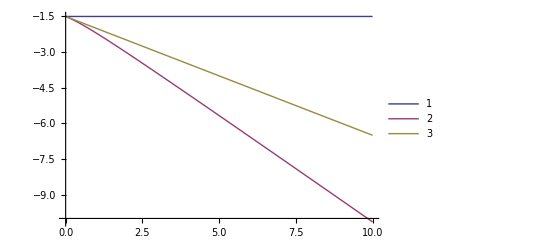

```mathematica
Plot[{E0,ENRELAX[t],ENSTIFF[t]},{t,0,10},PlotLegends->Automatic]
```